1) {x, y}, the parameter values over which the loop was iterated

2) {M1, M2, M3, M0, Mtau, 
MQ, MNR, tanβ, v, vevS, 
Atop, Abtm, Atau, An11, An12,
 An13, AlambdaN, Yn11, Yn12, Yn13, 
 lambda, lambdaN, kappa, PhisPI, Phi2PI, 
 ksi, Alambda, Akappa}, the input parameters
 
3) {χN-mass(5),  χC-mass(2), H+-mass(2), ν-mass(4), snu-mass(8), 
H0-mass(6), slep-mass(6), sup-mass(2), sdn-mass(2), stp-mass(2), 
sbt-mass(2)}, the mass eigenvalues, each of these is a vector in itself with the dimension noted in parentheses.

4) {χNre(5x5), χNim(5x5), 
χC-Ure(2x2),  χCU-im(2x2), χCV-re(2x2), χCV-im(2x2),  
νre(4x4), νim(4x4), 
H0(6x6), 
snu(8x8), 
slepCre(6x6), slepCim(6x6), 
sdown-re(2x2), sdown-im(2x2), sup-re(2x2), sup-im(2x2), stop-re(2x2), stop-im(2x2), sbottom-re(2x2), sbottom-im(2x2),
H+-(2x2)}, the mixing matrices, each of these is a nxn matrix with the dimensions noted in parentheses

5) {omega, CDM candidate name, Xf}, self explanatory

6) {cross section in pb, input channel, output channel}, cross sections for selected channels

7) CDM nucleon magic (amp = micromegas Amplitude, cs=cross section [pb])
{{n-cdm SI amp, n-anti-cdm SI amp, n-cdm SD amp, n-anti-cdm SD amp}, 
  {p-cdm SI amp, p-anti-cdm SI amp, p-cdm SD amp, p-anti-cdm SD amp}, 
  {n-cdm SI cs, n-anti-cdm SI cs, n-cdm SD cs, n-anti-cdm SD cs}, 
  {p-cdm SI cs, p-anti-cdm SI cs, p-cdm SD cs, p-anti-cdm SD cs}}
 
 8) Bsgamma ect
 
 9) {{Δa_e, Δa_μ, Δa_τ},
 {d_e, d_μ, d_τ}, 
 {BR( τ -> μ γ ), BR( τ -> e γ ), BR( μ -> e γ ) }}

```mathematica
file1=<<"/Users/ruppell/Math/temp/output-cpx.txt"; (* CP violating general data set *)
label1="Fig CPV";
```

```mathematica
file2=<<"/Users/ruppell/Math/temp/output-cpc.txt"; (* CP conserving general data set *)
label2="Fig no CP";
```

```mathematica
file3=<<"/Users/ruppell/Math/temp/output-CPtestXch0.txt"; 
label3="Fig χ0 LSP CPV";
```

```mathematica
file4=<<"/Users/ruppell/Math/temp/output-CPtestSnu.txt"; 
label4="Fig Snu LSP CPV";
```

```mathematica
SetOptions[ListPointPlot3D,{BoxRatios->{1,1,1},ImageSize->400}];
SetOptions[ListPlot,{ImageSize->400}];
SetOptions[Histogram,{ImageSize->400}];

mχ0mSnuRD=Transpose@{Abs@#[[;;,3,1,1]],#[[;;,3,5,1]],Log[10,#[[;;,6,1]]]}&;
mSnuRD=Transpose@{#[[;;,3,5,1]],Log[10,#[[;;,6,1]]]}&;
mχ0RD=Transpose@{Abs@#[[;;,3,1,1]],Log[10,#[[;;,6,1]]]}&;

mχ0mSnuRDopts=Sequence[AxesLabel->{"M_χ^0_1","M_snu_1","Ωh^2"},PlotRange->{{0,300},{0,500},{-6,2}}];
mSnuRDopts=Sequence[AxesLabel->{"M_snu_1","Ωh^2"},AspectRatio->1,PlotRange->{{0,300},Automatic}];
mχ0RDopts=Sequence[AxesLabel->{"M_χ^0_1","Ωh^2"},AspectRatio->1,PlotRange->{{0,300},Automatic}];
```

```mathematica
yesCPsnuLSP=Select[file1,#[[3,5,1]]<Abs@#[[3,1,1]]&];
yesCPχ0LSP=Select[file1,#[[3,5,1]]>Abs@#[[3,1,1]]&];
noCPsnuLSP=Select[file2,#[[3,5,1]]<Abs@#[[3,1,1]]&];
noCPχ0LSP=Select[file2,#[[3,5,1]]>Abs@#[[3,1,1]]&];
```

```mathematica
yesSnuRD=Select[yesCPsnuLSP,#[[6,1]]>0.1&&#[[6,1]]<0.12&];
yesχ0RD=Select[yesCPχ0LSP,#[[6,1]]>0.1&&#[[6,1]]<0.12&];
noSnuRD=Select[noCPsnuLSP,#[[6,1]]>0.1&&#[[6,1]]<0.12&];
noχ0RD=Select[noCPχ0LSP,#[[6,1]]>0.1&&#[[6,1]]<0.12&];
```

```mathematica
p1=ListPointPlot3D[mχ0mSnuRD[yesCPsnuLSP],PlotLabel->label1,mχ0mSnuRDopts];
p2=ListPointPlot3D[mχ0mSnuRD[yesCPχ0LSP],PlotLabel->label1,mχ0mSnuRDopts];
p3=ListPointPlot3D[mχ0mSnuRD[noCPsnuLSP],PlotLabel->label2,mχ0mSnuRDopts];
p4=ListPointPlot3D[mχ0mSnuRD[noCPχ0LSP],PlotLabel->label2,mχ0mSnuRDopts];
```

```mathematica
p5=ListPointPlot3D[mχ0mSnuRD[yesSnuRD],PlotLabel->label1,mχ0mSnuRDopts];
p6=ListPointPlot3D[mχ0mSnuRD[yesχ0RD],PlotLabel->label1,mχ0mSnuRDopts];
p7=ListPointPlot3D[mχ0mSnuRD[noSnuRD],PlotLabel->label2,mχ0mSnuRDopts];
p8=ListPointPlot3D[mχ0mSnuRD[noχ0RD],PlotLabel->label2,mχ0mSnuRDopts];
```

```mathematica
TableForm@{{p1,p2},{p3,p4}}
```

```mathematica
p9=ListPlot[{mSnuRD[yesCPsnuLSP],mSnuRD[noCPsnuLSP]},mSnuRDopts];
p10=ListPlot[{mχ0RD[yesCPχ0LSP],mχ0RD[noCPχ0LSP]},mχ0RDopts];
```

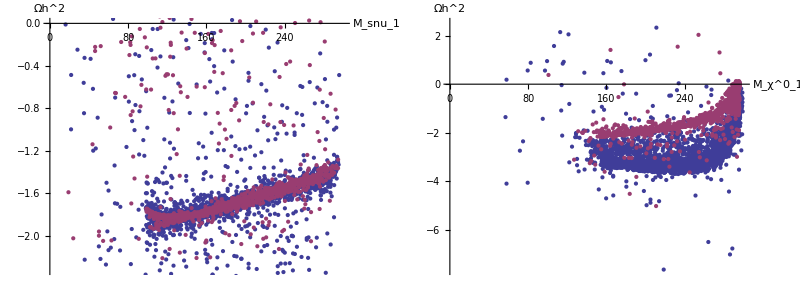

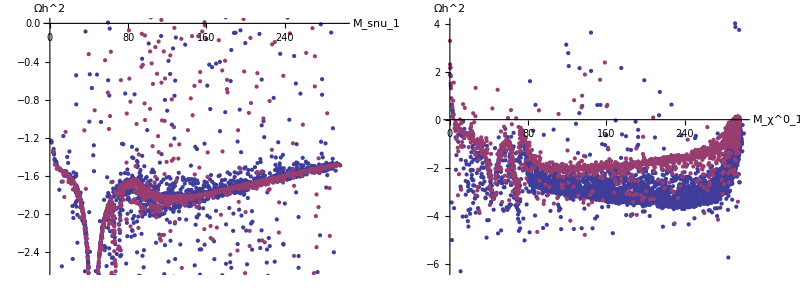

```mathematica
TableForm@{{p9,p10}}
```

```mathematica
TableForm@noSnuRD[[18,3]](* Selected spectrum from the CP cons. snu LSP data set *)
```

268.913 | -322.11 | 331.091 | 614.683 | 901.321 |  |  | 
306.513 | 614.809 |  |  |  |  |  | 
0 | 2775.22 |  |  |  |  |  | 
3.639×10^-12 | 0 | -4.20435×10^-10 | 215.761 |  |  |  | 
206.097 | 276.036 | 276.036 | 276.036 | 276.036 | 276.036 | 276.036 | 478.642
0.0000305176 | 126.996 | 674.636 | 1020.89 | 2774.3 | 2774.47 |  | 
279.346 | 286.883 | 286.883 | 287.43 | 287.43 | 294.771 |  | 
998.555 | 999.356 |  |  |  |  |  | 
1000.32 | 1001.76 |  |  |  |  |  | 
813.573 | 1180.61 |  |  |  |  |  | 
989.781 | 1012.2 |  |  |  |  |  |

```mathematica
TableForm@noχ0RD[[35,3]] (* Selected spectrum from the CP cons. χ0 LSP data set *)
```

282.087 | 350.71 | -351.792 | 615.669 | 663.715 |  |  | 
336.779 | 615.981 |  |  |  |  |  | 
0 | 3243.19 |  |  |  |  |  | 
1.86×10^-13 | 0 | -7.5351×10^-11 | 1200.43 |  |  |  | 
318.55 | 318.55 | 318.55 | 318.55 | 318.55 | 318.55 | 988.751 | 1383.83
-0.0000431584 | 125.573 | 387.364 | 933.579 | 3241.58 | 3241.61 |  | 
321.425 | 327.996 | 327.996 | 328.475 | 328.475 | 334.917 |  | 
998.554 | 999.356 |  |  |  |  |  | 
1000.32 | 1001.76 |  |  |  |  |  | 
813.6 | 1180.6 |  |  |  |  |  | 
987.027 | 1014.89 |  |  |  |  |  |

```mathematica
TableForm@Transpose@{{"Param",M1,M2,M3,M0,Mtau,MQ,MNR,tanβ,v,vevS,Atop,Abtm,Atau,An11,An12,An13,AlambdaN,Yn11,Yn12,Yn13,lambda,lambdaN,kappa,PhisPI,Phi2PI,ksi,Alambda,Akappa,mh1, mh2, mS},
Flatten@{"χ0 LSP",noχ0RD[[35,2]]},Flatten@{"snu LSP",noSnuRD[[18,2]]}}
```

Param | χ0 LSP | snu LSP
M1 | 300 | 300
M2 | 600 | 600
M3 | 1800 | 1800
M0 | 325.039 | 283.498
Mtau | 1.77 | 1.77
MQ | 1000 | 1000
MNR | 72.5716 | 298.721
tanβ | 33.3779 | 31.4067
v | 174 | 174
vevS | 1538.18 | 708.018
Atop | 1500 | 1500
Abtm | 1500 | 1500
Atau | -2500 | -2500
An11 | 0 | 0
An12 | 0 | 0
An13 | 0 | 0
AlambdaN | -720.485 | -878.818
Yn11 | 1/1000000 | 1/1000000
Yn12 | 1/1000000 | 1/1000000
Yn13 | 1/1000000 | 1/1000000
lambda | 0.225196 | 0.444565
lambdaN | 0.390213 | 0.15237
kappa | 0.214666 | 0.631268
PhisPI | 0 | 0
Phi2PI | 0 | 0
ksi | 0 | 0
Alambda | 577.305 | 330.288
Akappa | -879.602 | -776.533
mh1 | 3226.55 | 2759.34
mh2 | 0.+290.226 ⅈ | 0.+254.847 ⅈ
mS | 266.48 | 0.+240.208 ⅈ

Looking at which states change mass due to cp phases

```mathematica
plotNice=TableForm@{{Histogram[Abs@#1[[;;,##3]],#2],
ListPointPlot3D@Transpose@{#1[[;;,2,24]],#1[[;;,2,25]],Abs@#1[[;;,##3]]}},
{ListPlot@Transpose@{#1[[;;,2,25]],Abs@#1[[;;,##3]]},
ListPlot@Transpose@{#1[[;;,2,24]],Abs@#1[[;;,##3]]}}}&;
logPlotNice=TableForm@{{Histogram[Log[10,Abs@#1[[;;,##3]]],#2],
ListPointPlot3D@Transpose@{#1[[;;,2,24]],#1[[;;,2,25]],Log[10,Abs@#1[[;;,##3]]]}},
{ListPlot@Transpose@{#1[[;;,2,25]],Log[10,Abs@#1[[;;,##3]]]},
ListPlot@Transpose@{#1[[;;,2,24]],Log[10,Abs@#1[[;;,##3]]]}}}&;
```

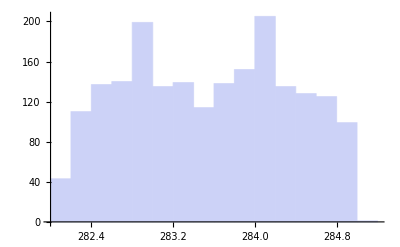
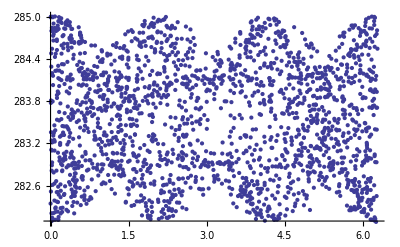
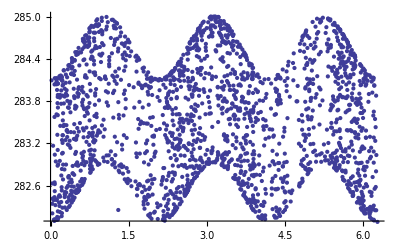
-Graphics- | -Graphics3D-
-Graphics- | -Graphics-

```mathematica
plotNice[file3,Automatic,3,1,1](* Lightest Neutralino *)
```

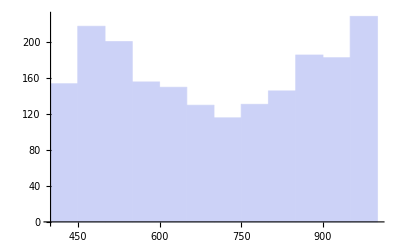
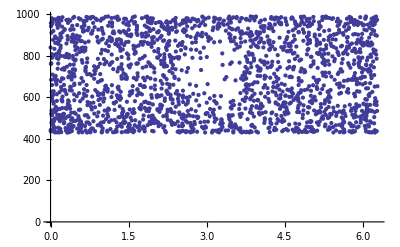
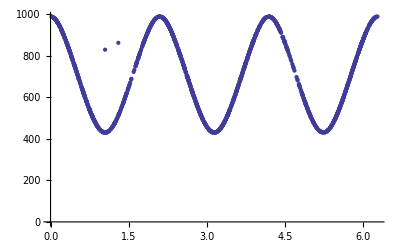
-Graphics- | -Graphics3D-
-Graphics- | -Graphics-

```mathematica
plotNice[file3,Automatic,3,5,7](* Lightest sneutrino *)
```

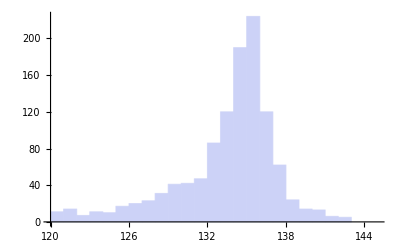
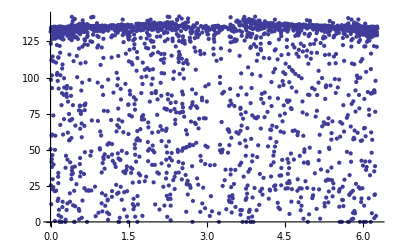
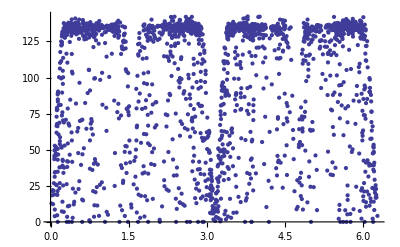
-Graphics- | -Graphics3D-
-Graphics- | -Graphics-

```mathematica
plotNice[file3,{120,145,1},3,6,2](* Lightest Higgs *)
```

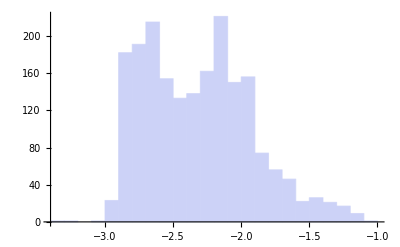
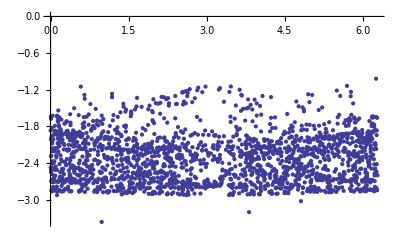
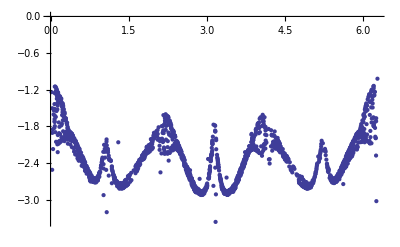
-Graphics- | -Graphics3D-
-Graphics- | -Graphics-

```mathematica
logPlotNice[file3,Automatic,6,1](* Relic Density *)
```

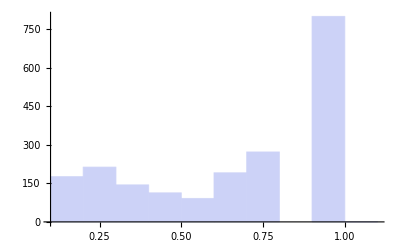
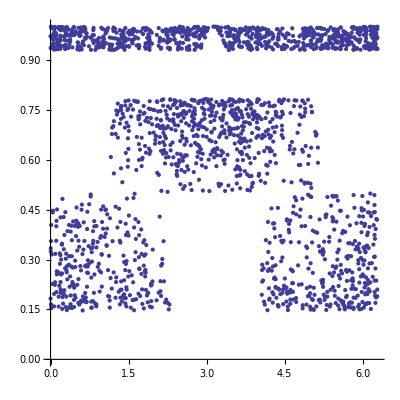
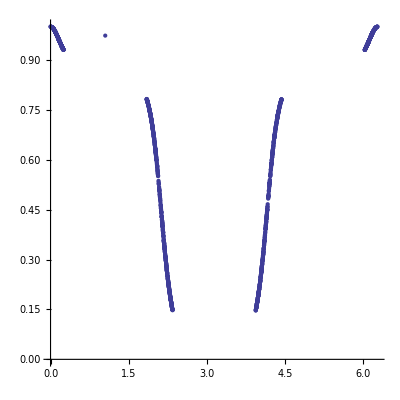
-Graphics- | -Graphics3D-
-Graphics- | -Graphics-

```mathematica
plotNice[file4,Automatic,4,10,1,4](* Lightest sneutrino r-h CP even component *)
```

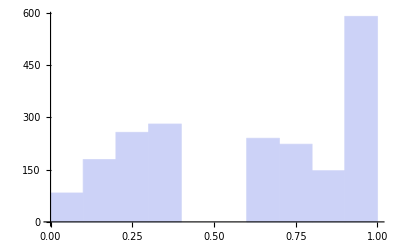
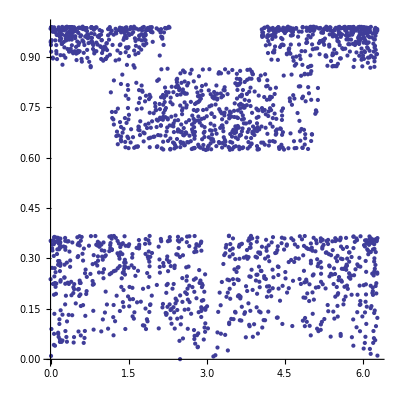
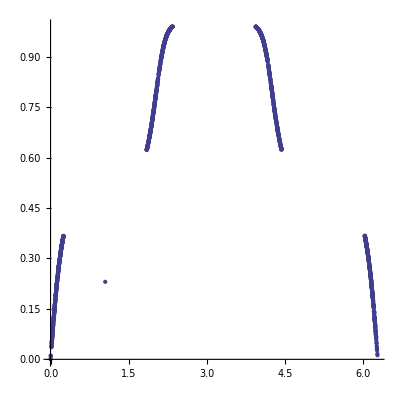
-Graphics- | -Graphics3D-
-Graphics- | -Graphics-

```mathematica
plotNice[file4,Automatic,4,10,1,8](* Lightest sneutrino r-h CP odd component *)
```